# Project Euler

## Problem 1 - Multiples of 3 and 5

If we list all the natural numbers below 10 that are multiples of 3 or 5, we get 3, 5, 6 and 9. The sum of these multiples is 23. Find the sum of all the multiples of 3 or 5 below 1000.

```mathematica
ClearAll[problem1,Nmax]
SetAttributes[problem1,Listable]
problem1[Nmax_]:=Plus@@(Union[Select[Range[Nmax],Mod[#,3]==0&],Select[Range[Nmax],Mod[#,5]==0&]])
```

```mathematica
problem1[999]
```

233168

```mathematica
problem1[{9,99,999,9999,99999}]
```

{23,2318,233168,23331668,2333316668}

## Problem 2 - Even Fibonacci numbers

Each new term in the Fibonacci sequence is generated by adding the previous two terms. By starting with 1 and 2, the first 10 terms will be:
1, 2, 3, 5, 8, 13, 21, 34, 55, 89, ...
By considering the terms in the Fibonacci sequence whose values do not exceed four million, find the sum of the even-valued terms.

```mathematica
ClearAll[list]
list=Fibonacci[Range[2,100]];
pos=Length[Select[(list/(4 10^6)//N)-1,#<0&]];
Plus@@Select[Fibonacci[Range[2,pos+1]],EvenQ]
```

4613732

## Problem 3 - Largest prime factor

The prime factors of 13195 are 5, 7, 13 and 29.
What is the largest prime factor of the number 600851475143 ?

```mathematica
Transpose[FactorInteger[600851475143]]⟦1⟧//Max
```

6857

## Problem 4 - Largest palindrome product

A palindromic number reads the same both ways. The largest palindrome made from the product of two 2-digit numbers is 9009 = 91 × 99.
Find the largest palindrome made from the product of two 3-digit numbers.

```mathematica
SetAttributes[palindromeQ,Listable]
palindromeQ[n_]:=(n//ToString//StringReverse)==ToString[n]
```

```mathematica
integers=Position[palindromeQ@Table[i j,{i,100,999},{j,100,999}],True];
```

```mathematica
Position[Plus@@@integers,Max[Plus@@@integers]]
```

{{2367},{2468}}

```mathematica
Print["The integers of three digits tha produce palindromes are "<>ToString@(integers⟦2367⟧+99)⟦1⟧<>", "<>ToString@(integers⟦2367⟧+99)⟦2⟧ <>" and their product is "<>ToString@(Times@@(integers⟦2367⟧+99))<>"."]
```

The integers of three digits tha produce palindromes are 913, 993 and their product is 906609.

## Problem 5 - Smallest multiple

2520 is the smallest number that can be divided by each of the numbers from 1 to 10 without any remainder.
What is the smallest positive number that is evenly divisible by all of the numbers from 1 to 20?

### Solution 1

```mathematica
nPrimes=20;
factors=FactorInteger[Range[nPrimes]]//Flatten[#,1]&//Union
orgfactors=Table[Cases[factors,{Prime[i],_}],{i,Length[Select[Prime[Range[nPrimes]],#<20&]]}]
Times@@Table[Prime[k]^(Max@(orgfactors⟦k⟧//Transpose)⟦2⟧),{k,Length[%]}]
```

{{1,1},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{5,1},{7,1},{11,1},{13,1},{17,1},{19,1}}

{{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2}},{{5,1}},{{7,1}},{{11,1}},{{13,1}},{{17,1}},{{19,1}}}

232792560

### Solution 2

```mathematica
factors=Flatten[FactorInteger/@Range[20],1];
theResult=Times@@Sequence[(#⟦1⟧)^(#⟦2⟧)&/@Normal[GroupBy[factors,First->Last,Max]]]
```

232792560

## Problem 6 - Sum square difference

The sum of the squares of the first ten natural numbers is,
1^2+ 2^2 + ... + 10^2 = 385
The square of the sum of the first ten natural numbers is,
(1 + 2 + ... + (10))^2 = 55^2 = 3025
Hence the difference between the sum of the squares of the first ten natural numbers and the square of the sum is 3025 − 385 = 2640.
Find the difference between the sum of the squares of the first one hundred natural numbers and the square of the sum.

```mathematica
((∑_(i=1)^n i)^2-∑_(i=1)^n i^2//Simplify)/.n->100
```

25164150

## Problem 7 - 10001st prime

By listing the first six prime numbers: 2, 3, 5, 7, 11, and 13, we can see that the 6th prime is 13.
What is the 10 001st prime number?

```mathematica
Prime[6]
```

13

```mathematica
Prime[10001]
```

104743

## Problem 8 - Largest product in a series

The four adjacent digits in the 1000-digit number that have the greatest product are 9 × 9 × 8 × 9 = 5832.

73167176531330624919225119674426574742355349194934
96983520312774506326239578318016984801869478851843
85861560789112949495459501737958331952853208805511
12540698747158523863050715693290963295227443043557
66896648950445244523161731856403098711121722383113
62229893423380308135336276614282806444486645238749
30358907296290491560440772390713810515859307960866
70172427121883998797908792274921901699720888093776
65727333001053367881220235421809751254540594752243
52584907711670556013604839586446706324415722155397
53697817977846174064955149290862569321978468622482
83972241375657056057490261407972968652414535100474
82166370484403199890008895243450658541227588666881
16427171479924442928230863465674813919123162824586
17866458359124566529476545682848912883142607690042
24219022671055626321111109370544217506941658960408
07198403850962455444362981230987879927244284909188
84580156166097919133875499200524063689912560717606
05886116467109405077541002256983155200055935729725
71636269561882670428252483600823257530420752963450

Find the thirteen adjacent digits in the 1000-digit number that have the greatest product. What is the value of this product?

```mathematica
number="7316717653133062491922511967442657474235534919493496983520312774506326239578318016984801869478851843858615607891129494954595017379583319528532088055111254069874715852386305071569329096329522744304355766896648950445244523161731856403098711121722383113622298934233803081353362766142828064444866452387493035890729629049156044077239071381051585930796086670172427121883998797908792274921901699720888093776657273330010533678812202354218097512545405947522435258490771167055601360483958644670632441572215539753697817977846174064955149290862569321978468622482839722413756570560574902614079729686524145351004748216637048440319989000889524345065854122758866688116427171479924442928230863465674813919123162824586178664583591245665294765456828489128831426076900422421902267105562632111110937054421750694165896040807198403850962455444362981230987879927244284909188845801561660979191338754992005240636899125607176060588611646710940507754100225698315520005593572972571636269561882670428252483600823257530420752963450";
```

### Solution 1

```mathematica
multiplyDigits[string_]:=Times@@Table[ToExpression@StringTake[string,{i}],{i,StringLength[string]}]
```

```mathematica
step=13;
multiplyDigits/@Table[StringTake[number,{i,step+i-1}],{i,1,StringLength[number]-step}]//Max
```

23514624000

### Solution 2

```mathematica
digits=IntegerDigits[number//ToExpression];
theResult=Max[Table[Times@@Sequence[digits⟦k;;k+step-1⟧],{k,1000-(step-1)}]]
```

23514624000

## Problem 9 - Special Pythagorean triplet

A Pythagorean triplet is a set of three natural numbers, a < b < c, for which,
a^2 + b^2 = c^2
For example, 3^2 + 4^2 = 9 + 16 = 25 = 5^2.
There exists exactly one Pythagorean triplet for which a + b + c = 1000.
Find the product abc.

```mathematica
perimeter=1000;
pythagoreanTriplet=({a,b,c}/.Solve[{a^2+b^2==c^2,a+b+c==perimeter,a>0,b>0,c>0,c>b,b>a},{a,b,c},Integers])⟦1⟧
Times@@pythagoreanTriplet
```

{200,375,425}

31875000

```mathematica
table=ParallelTable[{k,({a,b,c}/.Solve[{a^2+b^2==c^2,a+b+c==k,a>0,b>0,c>0,c>b,b>a},{a,b,c},Integers])⟦1⟧/.a->"-"},{k,1,5000,1}];
TableForm[(Select[table,FreeQ[#,"-"]&]//Transpose),TableHeadings->{{"Perimeter","Pythagorean Triplet"},None}]
```

Perimeter | 12 | 24 | 30 | 36 | 40 | 48 | 56 | 60 | 70 | 72 | 80 | 84 | 90 | 96 | 108 | 112 | 120 | 126 | 132 | 140 | 144 | 150 | 154 | 156 | 160 | 168 | 176 | 180 | 182 | 192 | 198 | 200 | 204 | 208 | 210 | 216 | 220 | 224 | 228 | 234 | 240 | 252 | 260 | 264 | 270 | 276 | 280 | 286 | 288 | 300 | 306 | 308 | 312 | 320 | 324 | 330 | 336 | 340 | 348 | 350 | 352 | 360 | 364 | 372 | 374 | 378 | 380 | 384 | 390 | 392 | 396 | 400 | 408 | 416 | 418 | 420 | 432 | 440 | 442 | 444 | 448 | 450 | 456 | 462 | 468 | 476 | 480 | 490 | 492 | 494 | 504 | 510 | 516 | 520 | 528 | 532 | 540 | 544 | 546 | 552 | 560 | 564 | 570 | 572 | 576 | 588 | 594 | 598 | 600 | 608 | 612 | 616 | 624 | 630 | 636 | 640 | 644 | 646 | 648 | 650 | 660 | 672 | 680 | 684 | 690 | 696 | 700 | 702 | 704 | 708 | 714 | 720 | 728 | 732 | 736 | 744 | 748 | 750 | 756 | 760 | 768 | 770 | 780 | 782 | 784 | 792 | 798 | 800 | 804 | 810 | 816 | 828 | 832 | 836 | 840 | 850 | 852 | 858 | 864 | 870 | 874 | 876 | 880 | 882 | 884 | 888 | 896 | 900 | 910 | 912 | 918 | 920 | 924 | 928 | 930 | 936 | 948 | 950 | 952 | 960 | 966 | 972 | 980 | 984 | 986 | 988 | 990 | 992 | 996 | 1000 | 1008 | 1012 | 1020 | 1026 | 1032 | 1040 | 1044 | 1050 | 1054 | 1056 | 1064 | 1068 | 1078 | 1080 | 1088 | 1092 | 1100 | 1102 | 1104 | 1110 | 1116 | 1120 | 1122 | 1128 | 1134 | 1140 | 1144 | 1150 | 1152 | 1160 | 1164 | 1170 | 1176 | 1178 | 1188 | 1190 | 1196 | 1200 | 1212 | 1216 | 1218 | 1224 | 1230 | 1232 | 1236 | 1240 | 1242 | 1248 | 1254 | 1260 | 1272 | 1274 | 1276 | 1280 | 1284 | 1288 | 1290 | 1292 | 1296 | 1300 | 1302 | 1308 | 1320 | 1326 | 1330 | 1332 | 1334 | 1344 | 1350 | 1356 | 1360 | 1364 | 1368 | 1380 | 1386 | 1392 | 1400 | 1404 | 1406 | 1408 | 1410 | 1416 | 1426 | 1428 | 1430 | 1440 | 1450 | 1452 | 1456 | 1464 | 1470 | 1472 | 1476 | 1480 | 1482 | 1488 | 1496 | 1500 | 1508 | 1512 | 1518 | 1520 | 1524 | 1530 | 1536 | 1540 | 1548 | 1550 | 1554 | 1560 | 1564 | 1566 | 1568 | 1572 | 1584 | 1590 | 1596 | 1600 | 1608 | 1610 | 1612 | 1620 | 1624 | 1628 | 1632 | 1638 | 1640 | 1644 | 1650 | 1656 | 1664 | 1668 | 1672 | 1674 | 1680 | 1692 | 1694 | 1700 | 1702 | 1704 | 1710 | 1716 | 1720 | 1722 | 1728 | 1736 | 1740 | 1748 | 1750 | 1752 | 1760 | 1764 | 1768 | 1770 | 1776 | 1782 | 1788 | 1792 | 1794 | 1798 | 1800 | 1804 | 1812 | 1820 | 1824 | 1830 | 1836 | 1840 | 1848 | 1850 | 1856 | 1860 | 1870 | 1872 | 1880 | 1884 | 1886 | 1890 | 1892 | 1896 | 1900 | 1904 | 1908 | 1914 | 1920 | 1924 | 1932 | 1936 | 1938 | 1944 | 1950 | 1956 | 1960 | 1968 | 1972 | 1976 | 1978 | 1980 | 1984 | 1992 | 1998 | 2000 | 2002 | 2004 | 2010 | 2016 | 2024 | 2028 | 2030 | 2040 | 2046 | 2050 | 2052 | 2064 | 2070 | 2072 | 2076 | 2080 | 2088 | 2090 | 2100 | 2106 | 2108 | 2112 | 2120 | 2124 | 2128 | 2130 | 2132 | 2136 | 2142 | 2146 | 2148 | 2150 | 2156 | 2160 | 2170 | 2172 | 2176 | 2178 | 2184 | 2190 | 2196 | 2200 | 2204 | 2208 | 2210 | 2214 | 2220 | 2232 | 2236 | 2240 | 2244 | 2250 | 2256 | 2262 | 2268 | 2280 | 2288 | 2292 | 2294 | 2296 | 2300 | 2304 | 2310 | 2316 | 2320 | 2322 | 2328 | 2340 | 2346 | 2350 | 2352 | 2356 | 2360 | 2364 | 2366 | 2368 | 2370 | 2376 | 2378 | 2380 | 2388 | 2392 | 2394 | 2400 | 2408 | 2412 | 2418 | 2420 | 2424 | 2430 | 2432 | 2436 | 2440 | 2442 | 2444 | 2448 | 2450 | 2460 | 2464 | 2470 | 2472 | 2480 | 2484 | 2490 | 2494 | 2496 | 2508 | 2516 | 2520 | 2532 | 2538 | 2542 | 2544 | 2548 | 2550 | 2552 | 2556 | 2560 | 2568 | 2574 | 2576 | 2580 | 2584 | 2590 | 2592 | 2600 | 2604 | 2610 | 2616 | 2618 | 2622 | 2624 | 2628 | 2632 | 2640 | 2646 | 2652 | 2660 | 2664 | 2666 | 2668 | 2670 | 2676 | 2680 | 2688 | 2700 | 2704 | 2706 | 2712 | 2720 | 2724 | 2726 | 2728 | 2730 | 2736 | 2744 | 2748 | 2752 | 2754 | 2760 | 2772 | 2784 | 2788 | 2790 | 2796 | 2800 | 2808 | 2812 | 2816 | 2820 | 2832 | 2838 | 2840 | 2842 | 2844 | 2850 | 2852 | 2856 | 2860 | 2862 | 2868 | 2870 | 2880 | 2886 | 2892 | 2898 | 2900 | 2904 | 2910 | 2912 | 2914 | 2916 | 2920 | 2924 | 2926 | 2928 | 2940 | 2944 | 2952 | 2958 | 2960 | 2964 | 2968 | 2970 | 2976 | 2988 | 2990 | 2992 | 3000 | 3008 | 3010 | 3012 | 3016 | 3024 | 3030 | 3034 | 3036 | 3038 | 3040 | 3042 | 3048 | 3060 | 3072 | 3074 | 3078 | 3080 | 3084 | 3090 | 3094 | 3096 | 3100 | 3102 | 3108 | 3116 | 3120 | 3128 | 3132 | 3136 | 3144 | 3146 | 3150 | 3156 | 3160 | 3162 | 3168 | 3180 | 3182 | 3190 | 3192 | 3196 | 3198 | 3200 | 3204 | 3210 | 3216 | 3220 | 3224 | 3228 | 3230 | 3234 | 3240 | 3248 | 3250 | 3252 | 3256 | 3264 | 3268 | 3270 | 3276 | 3280 | 3286 | 3288 | 3290 | 3300 | 3304 | 3306 | 3312 | 3320 | 3324 | 3328 | 3330 | 3332 | 3336 | 3344 | 3348 | 3354 | 3360 | 3366 | 3372 | 3380 | 3384 | 3388 | 3390 | 3392 | 3396 | 3400 | 3402 | 3404 | 3408 | 3410 | 3416 | 3420 | 3430 | 3432 | 3440 | 3444 | 3450 | 3456 | 3458 | 3468 | 3472 | 3478 | 3480 | 3492 | 3496 | 3498 | 3500 | 3504 | 3510 | 3516 | 3520 | 3526 | 3528 | 3534 | 3536 | 3540 | 3542 | 3552 | 3560 | 3564 | 3570 | 3572 | 3576 | 3584 | 3588 | 3596 | 3600 | 3604 | 3608 | 3612 | 3624 | 3626 | 3630 | 3636 | 3640 | 3648 | 3654 | 3658 | 3660 | 3666 | 3672 | 3680 | 3684 | 3690 | 3696 | 3700 | 3708 | 3710 | 3712 | 3718 | 3720 | 3724 | 3726 | 3732 | 3740 | 3744 | 3750 | 3752 | 3756 | 3760 | 3762 | 3768 | 3772 | 3774 | 3776 | 3780 | 3782 | 3784 | 3792 | 3800 | 3804 | 3808 | 3810 | 3816 | 3822 | 3828 | 3840 | 3848 | 3850 | 3852 | 3854 | 3864 | 3870 | 3872 | 3876 | 3880 | 3888 | 3894 | 3900 | 3904 | 3906 | 3910 | 3912 | 3920 | 3922 | 3924 | 3930 | 3936 | 3944 | 3948 | 3952 | 3956 | 3960 | 3968 | 3972 | 3976 | 3978 | 3984 | 3990 | 3996 | 4000 | 4002 | 4004 | 4008 | 4012 | 4018 | 4020 | 4026 | 4028 | 4032 | 4040 | 4042 | 4044 | 4048 | 4050 | 4056 | 4060 | 4068 | 4070 | 4080 | 4088 | 4092 | 4100 | 4104 | 4110 | 4114 | 4116 | 4120 | 4128 | 4130 | 4134 | 4136 | 4140 | 4144 | 4148 | 4152 | 4158 | 4160 | 4164 | 4170 | 4176 | 4180 | 4182 | 4186 | 4188 | 4200 | 4212 | 4214 | 4216 | 4218 | 4224 | 4230 | 4236 | 4240 | 4248 | 4250 | 4256 | 4260 | 4264 | 4270 | 4272 | 4278 | 4280 | 4284 | 4290 | 4292 | 4296 | 4300 | 4308 | 4312 | 4320 | 4324 | 4332 | 4340 | 4344 | 4346 | 4350 | 4352 | 4356 | 4360 | 4366 | 4368 | 4370 | 4380 | 4386 | 4392 | 4400 | 4404 | 4408 | 4410 | 4416 | 4420 | 4424 | 4428 | 4440 | 4446 | 4452 | 4464 | 4466 | 4470 | 4472 | 4476 | 4480 | 4484 | 4488 | 4500 | 4508 | 4510 | 4512 | 4514 | 4520 | 4522 | 4524 | 4530 | 4536 | 4548 | 4550 | 4554 | 4556 | 4558 | 4560 | 4572 | 4576 | 4584 | 4588 | 4590 | 4592 | 4596 | 4598 | 4600 | 4602 | 4606 | 4608 | 4620 | 4632 | 4636 | 4640 | 4644 | 4648 | 4650 | 4656 | 4662 | 4664 | 4668 | 4674 | 4680 | 4690 | 4692 | 4698 | 4700 | 4704 | 4710 | 4712 | 4716 | 4720 | 4728 | 4730 | 4732 | 4736 | 4740 | 4750 | 4752 | 4756 | 4758 | 4760 | 4764 | 4770 | 4774 | 4776 | 4784 | 4788 | 4794 | 4800 | 4810 | 4812 | 4816 | 4824 | 4830 | 4836 | 4838 | 4840 | 4848 | 4860 | 4862 | 4864 | 4872 | 4876 | 4880 | 4884 | 4888 | 4890 | 4896 | 4900 | 4902 | 4908 | 4914 | 4920 | 4928 | 4930 | 4932 | 4940 | 4944 | 4950 | 4956 | 4958 | 4960 | 4968 | 4970 | 4980 | 4982 | 4984 | 4988 | 4992 | 4998 | 5000
Pythagorean Triplet | 3
4
5 | 6
8
10 | 5
12
13 | 9
12
15 | 8
15
17 | 12
16
20 | 7
24
25 | 10
24
26 | 20
21
29 | 18
24
30 | 16
30
34 | 12
35
37 | 9
40
41 | 24
32
40 | 27
36
45 | 14
48
50 | 20
48
52 | 28
45
53 | 11
60
61 | 40
42
58 | 16
63
65 | 25
60
65 | 33
56
65 | 39
52
65 | 32
60
68 | 21
72
75 | 48
55
73 | 18
80
82 | 13
84
85 | 48
64
80 | 36
77
85 | 40
75
85 | 51
68
85 | 39
80
89 | 35
84
91 | 54
72
90 | 20
99
101 | 28
96
100 | 57
76
95 | 65
72
97 | 15
112
113 | 36
105
111 | 60
91
109 | 22
120
122 | 27
120
123 | 69
92
115 | 35
120
125 | 44
117
125 | 32
126
130 | 50
120
130 | 17
144
145 | 66
112
130 | 24
143
145 | 64
120
136 | 81
108
135 | 55
132
143 | 42
144
150 | 51
140
149 | 87
116
145 | 100
105
145 | 96
110
146 | 36
160
164 | 26
168
170 | 93
124
155 | 85
132
157 | 84
135
159 | 19
180
181 | 96
128
160 | 52
165
173 | 49
168
175 | 33
180
183 | 80
150
170 | 102
136
170 | 78
160
178 | 57
176
185 | 28
195
197 | 48
189
195 | 40
198
202 | 104
153
185 | 111
148
185 | 56
192
200 | 45
200
205 | 95
168
193 | 21
220
221 | 117
156
195 | 84
187
205 | 30
224
226 | 140
147
203 | 123
164
205 | 133
156
205 | 63
216
225 | 60
221
229 | 129
172
215 | 104
195
221 | 44
240
244 | 140
171
221 | 54
240
246 | 32
255
257 | 39
252
255 | 23
264
265 | 70
240
250 | 141
188
235 | 95
228
247 | 88
234
250 | 64
252
260 | 84
245
259 | 108
231
255 | 69
260
269 | 100
240
260 | 96
247
265 | 34
288
290 | 77
264
275 | 48
286
290 | 63
280
287 | 159
212
265 | 128
240
272 | 115
252
277 | 68
285
293 | 162
216
270 | 25
312
313 | 55
300
305 | 84
288
300 | 102
280
298 | 36
323
325 | 115
276
299 | 174
232
290 | 75
308
317 | 195
216
291 | 192
220
292 | 177
236
295 | 136
273
305 | 45
336
339 | 52
336
340 | 183
244
305 | 207
224
305 | 186
248
310 | 170
264
314 | 125
300
325 | 27
364
365 | 38
360
362 | 192
256
320 | 165
280
325 | 104
330
346 | 204
253
325 | 98
336
350 | 66
360
366 | 76
357
365 | 160
300
340 | 201
268
335 | 81
360
369 | 204
272
340 | 180
299
349 | 156
320
356 | 114
352
370 | 40
399
401 | 225
272
353 | 213
284
355 | 132
351
375 | 96
378
390 | 29
420
421 | 152
345
377 | 219
292
365 | 80
396
404 | 196
315
371 | 208
306
370 | 222
296
370 | 112
384
400 | 90
400
410 | 65
420
425 | 190
336
386 | 51
432
435 | 120
391
409 | 42
440
442 | 87
416
425 | 155
372
403 | 72
429
435 | 237
316
395 | 228
325
397 | 119
408
425 | 60
448
452 | 84
437
445 | 243
324
405 | 280
294
406 | 246
328
410 | 145
408
433 | 266
312
410 | 99
440
451 | 31
480
481 | 249
332
415 | 200
375
425 | 112
441
455 | 44
483
485 | 120
442
458 | 297
304
425 | 258
344
430 | 195
400
445 | 203
396
445 | 168
425
457 | 93
476
485 | 88
480
488 | 133
456
475 | 267
356
445 | 231
392
455 | 108
480
492 | 64
510
514 | 78
504
510 | 100
495
505 | 261
380
461 | 46
528
530 | 185
444
481 | 155
468
493 | 140
480
500 | 33
544
545 | 282
376
470 | 252
405
477 | 57
540
543 | 176
468
500 | 92
525
533 | 128
504
520 | 232
435
493 | 291
388
485 | 117
520
533 | 147
504
525 | 217
456
505 | 99
540
549 | 340
357
493 | 138
520
538 | 48
575
577 | 303
404
505 | 192
494
530 | 336
377
505 | 68
576
580 | 205
492
533 | 154
528
550 | 309
412
515 | 248
465
527 | 184
513
545 | 96
572
580 | 165
532
557 | 35
612
613 | 318
424
530 | 91
588
595 | 308
435
533 | 256
480
544 | 321
428
535 | 161
552
575 | 215
516
559 | 136
570
586 | 144
567
585 | 50
624
626 | 341
420
541 | 327
436
545 | 110
600
610 | 312
459
555 | 105
608
617 | 333
444
555 | 276
493
565 | 168
576
600 | 100
621
629 | 339
452
565 | 204
560
596 | 396
403
565 | 72
646
650 | 230
552
598 | 63
660
663 | 240
551
601 | 150
616
634 | 52
675
677 | 37
684
685 | 384
440
584 | 235
564
611 | 354
472
590 | 368
465
593 | 204
595
629 | 220
585
625 | 90
672
678 | 200
609
641 | 121
660
671 | 104
672
680 | 366
488
610 | 245
588
637 | 414
448
610 | 369
492
615 | 111
680
689 | 399
468
615 | 336
527
625 | 340
528
628 | 250
600
650 | 156
667
685 | 54
728
730 | 429
460
629 | 76
720
724 | 381
508
635 | 85
720
725 | 384
512
640 | 140
693
707 | 387
516
645 | 300
589
661 | 185
672
697 | 39
760
761 | 408
506
650 | 108
725
733 | 196
672
700 | 393
524
655 | 132
720
732 | 265
636
689 | 152
714
730 | 320
600
680 | 402
536
670 | 385
552
673 | 260
651
701 | 162
720
738 | 56
783
785 | 259
660
709 | 96
765
771 | 117
756
765 | 328
615
697 | 411
548
685 | 275
660
715 | 69
792
795 | 312
640
712 | 417
556
695 | 228
704
740 | 216
713
745 | 80
798
802 | 423
564
705 | 363
616
715 | 255
700
745 | 333
644
725 | 426
568
710 | 171
760
779 | 143
780
793 | 344
645
731 | 41
840
841 | 192
756
780 | 168
775
793 | 58
840
842 | 304
690
754 | 500
525
725 | 438
584
730 | 160
792
808 | 252
735
777 | 416
612
740 | 295
708
767 | 407
624
745 | 324
693
765 | 447
596
745 | 224
768
800 | 207
780
807 | 116
837
845 | 180
800
820 | 123
836
845 | 453
604
755 | 130
840
850 | 288
741
795 | 305
732
793 | 102
864
870 | 240
782
818 | 84
880
884 | 481
600
769 | 174
832
850 | 60
899
901 | 425
660
785 | 144
858
870 | 376
705
799 | 471
628
785 | 205
828
853 | 189
840
861 | 43
924
925 | 474
632
790 | 95
900
905 | 238
816
850 | 477
636
795 | 232
825
857 | 120
896
904 | 555
572
797 | 168
874
890 | 528
605
803 | 204
855
879 | 486
648
810 | 75
936
939 | 489
652
815 | 245
840
875 | 287
816
865 | 290
816
866 | 532
624
820 | 129
920
929 | 165
900
915 | 62
960
962 | 498
664
830 | 540
629
829 | 400
750
850 | 143
924
935 | 501
668
835 | 335
804
871 | 224
882
910 | 88
966
970 | 507
676
845 | 348
805
877 | 240
884
916 | 124
957
965 | 369
800
881 | 108
969
975 | 215
912
937 | 45
1012
1013 | 259
888
925 | 519
692
865 | 390
800
890 | 406
792
890 | 285
880
925 | 140
975
985 | 585
648
873 | 186
952
970 | 64
1023
1025 | 424
795
901 | 531
708
885 | 266
912
950 | 355
852
923 | 451
780
901 | 534
712
890 | 119
1008
1015 | 464
777
905 | 537
716
895 | 301
900
949 | 462
784
910 | 135
1008
1017 | 248
945
977 | 543
724
905 | 128
1020
1028 | 396
847
935 | 156
1008
1020 | 365
876
949 | 549
732
915 | 200
990
1010 | 522
760
922 | 92
1056
1060 | 520
765
925 | 533
756
925 | 370
888
962 | 310
936
986 | 387
884
965 | 192
1015
1033 | 66
1088
1090 | 225
1000
1025 | 47
1104
1105 | 580
741
941 | 81
1092
1095 | 114
1080
1086 | 352
936
1000 | 573
764
955 | 372
925
997 | 287
984
1025 | 184
1050
1066 | 256
1008
1040 | 105
1100
1105 | 579
772
965 | 464
870
986 | 473
864
985 | 582
776
970 | 234
1040
1066 | 612
759
975 | 141
1100
1109 | 294
1008
1050 | 434
912
1010 | 472
885
1003 | 591
788
985 | 169
1092
1105 | 320
999
1049 | 395
948
1027 | 198
1080
1098 | 696
697
985 | 68
1155
1157 | 597
796
995 | 276
1040
1076 | 228
1071
1095 | 96
1150
1154 | 301
1032
1075 | 603
804
1005 | 496
897
1025 | 220
1089
1111 | 606
808
1010 | 243
1080
1107 | 384
988
1060 | 348
1015
1073 | 488
915
1037 | 264
1073
1105 | 235
1092
1117 | 136
1152
1160 | 49
1200
1201 | 410
984
1066 | 308
1056
1100 | 665
780
1025 | 618
824
1030 | 496
930
1054 | 368
1026
1090 | 415
996
1079 | 645
812
1037 | 192
1144
1160 | 209
1140
1159 | 204
1147
1165 | 70
1224
1226 | 633
844
1055 | 329
1080
1129 | 620
861
1061 | 636
848
1060 | 147
1196
1205 | 300
1105
1145 | 616
870
1066 | 639
852
1065 | 512
960
1088 | 642
856
1070 | 396
1053
1125 | 322
1104
1150 | 430
1032
1118 | 272
1140
1172 | 140
1221
1229 | 288
1134
1170 | 100
1248
1252 | 372
1085
1147 | 87
1260
1263 | 654
872
1090 | 561
952
1105 | 456
1035
1131 | 576
943
1105 | 657
876
1095 | 329
1128
1175 | 165
1232
1243 | 245
1188
1213 | 51
1300
1301 | 133
1260
1267 | 72
1295
1297 | 744
817
1105 | 552
986
1130 | 445
1068
1157 | 669
892
1115 | 536
1005
1139 | 336
1152
1200 | 200
1242
1258 | 507
1040
1157 | 528
1025
1153 | 678
904
1130 | 160
1275
1285 | 681
908
1135 | 517
1044
1165 | 792
806
1130 | 195
1260
1275 | 144
1292
1300 | 343
1176
1225 | 687
916
1145 | 704
903
1145 | 153
1296
1305 | 115
1320
1325 | 126
1320
1326 | 261
1248
1275 | 476
1107
1205 | 279
1240
1271 | 699
932
1165 | 300
1232
1268 | 104
1350
1354 | 74
1368
1370 | 768
880
1168 | 470
1128
1222 | 708
944
1180 | 660
989
1189 | 568
1065
1207 | 441
1160
1241 | 711
948
1185 | 475
1140
1235 | 736
930
1186 | 255
1288
1313 | 260
1287
1313 | 53
1404
1405 | 717
956
1195 | 420
1189
1261 | 180
1344
1356 | 148
1365
1373 | 723
964
1205 | 252
1311
1335 | 400
1218
1282 | 242
1320
1342 | 485
1164
1261 | 208
1344
1360 | 705
992
1217 | 729
972
1215 | 584
1095
1241 | 612
1075
1237 | 399
1232
1295 | 732
976
1220 | 196
1365
1379 | 828
896
1220 | 360
1271
1321 | 357
1276
1325 | 222
1360
1378 | 76
1443
1445 | 159
1400
1409 | 297
1320
1353 | 93
1440
1443 | 747
996
1245 | 345
1300
1345 | 680
1056
1256 | 500
1200
1300 | 799
960
1249 | 560
1161
1289 | 753
1004
1255 | 312
1334
1370 | 108
1456
1460 | 505
1212
1313 | 296
1353
1385 | 132
1449
1455 | 637
1116
1285 | 152
1440
1448 | 845
936
1261 | 762
1016
1270 | 170
1440
1450 | 768
1024
1280 | 265
1392
1417 | 891
912
1275 | 55
1512
1513 | 771
1028
1285 | 515
1236
1339 | 221
1428
1445 | 504
1247
1345 | 600
1178
1322 | 893
924
1285 | 370
1344
1394 | 228
1435
1453 | 78
1520
1522 | 816
1012
1300 | 216
1450
1466 | 392
1344
1400 | 786
1048
1310 | 484
1287
1375 | 315
1400
1435 | 789
1052
1315 | 632
1185
1343 | 279
1428
1455 | 264
1440
1464 | 371
1380
1429 | 444
1333
1405 | 165
1508
1517 | 304
1428
1460 | 884
987
1325 | 156
1517
1525 | 640
1200
1360 | 801
1068
1335 | 535
1284
1391 | 804
1072
1340 | 575
1260
1385 | 520
1302
1402 | 807
1076
1345 | 340
1425
1465 | 147
1540
1547 | 324
1440
1476 | 112
1566
1570 | 125
1560
1565 | 813
1084
1355 | 518
1320
1418 | 192
1530
1542 | 380
1419
1469 | 545
1308
1417 | 234
1512
1530 | 80
1599
1601 | 477
1364
1445 | 822
1096
1370 | 840
1081
1369 | 275
1500
1525 | 413
1416
1475 | 57
1624
1625 | 138
1584
1590 | 664
1245
1411 | 831
1108
1385 | 624
1280
1424 | 333
1480
1517 | 588
1309
1435 | 834
1112
1390 | 456
1408
1480 | 432
1426
1490 | 312
1505
1537 | 160
1596
1604 | 99
1632
1635 | 843
1124
1405 | 780
1183
1417 | 792
1175
1417 | 726
1232
1430 | 565
1356
1469 | 583
1344
1465 | 849
1132
1415 | 510
1400
1490 | 756
1215
1431 | 666
1288
1450 | 852
1136
1420 | 385
1488
1537 | 427
1464
1525 | 171
1620
1629 | 980
1029
1421 | 264
1573
1595 | 240
1591
1609 | 82
1680
1682 | 276
1575
1599 | 384
1512
1560 | 247
1596
1615 | 867
1156
1445 | 336
1550
1586 | 740
1269
1469 | 116
1680
1684 | 873
1164
1455 | 608
1380
1508 | 689
1320
1489 | 375
1540
1585 | 876
1168
1460 | 351
1560
1599 | 879
1172
1465 | 320
1584
1616 | 164
1677
1685 | 441
1512
1575 | 285
1612
1637 | 663
1360
1513 | 59
1740
1741 | 759
1288
1495 | 814
1248
1490 | 712
1335
1513 | 297
1620
1647 | 420
1547
1603 | 684
1363
1525 | 894
1192
1490 | 448
1536
1600 | 414
1560
1614 | 232
1674
1690 | 144
1725
1731 | 795
1292
1517 | 246
1672
1690 | 84
1763
1765 | 906
1208
1510 | 888
1225
1513 | 605
1452
1573 | 909
1212
1515 | 260
1680
1700 | 399
1600
1649 | 812
1305
1537 | 177
1736
1745 | 610
1464
1586 | 624
1457
1585 | 204
1728
1740 | 480
1564
1636 | 921
1228
1535 | 328
1665
1697 | 168
1760
1768 | 962
1200
1538 | 927
1236
1545 | 901
1260
1549 | 348
1664
1700 | 572
1521
1625 | 120
1798
1802 | 836
1323
1565 | 552
1539
1635 | 933
1244
1555 | 340
1683
1717 | 288
1716
1740 | 625
1500
1625 | 469
1608
1675 | 939
1252
1565 | 560
1551
1649 | 495
1596
1671 | 942
1256
1570 | 410
1656
1706 | 1036
1173
1565 | 295
1728
1753 | 105
1836
1839 | 61
1860
1861 | 86
1848
1850 | 948
1264
1580 | 190
1800
1810 | 951
1268
1585 | 224
1785
1799 | 635
1524
1651 | 954
1272
1590 | 273
1764
1785 | 319
1740
1769 | 240
1792
1808 | 1110
1144
1594 | 825
1400
1625 | 963
1284
1605 | 492
1645
1717 | 161
1848
1855 | 172
1845
1853 | 1056
1210
1606 | 408
1710
1758 | 776
1455
1649 | 432
1701
1755 | 413
1716
1765 | 150
1872
1878 | 183
1856
1865 | 868
1395
1643 | 1020
1265
1625 | 978
1304
1630 | 490
1680
1750 | 1113
1184
1625 | 981
1308
1635 | 655
1572
1703 | 574
1632
1730 | 580
1632
1732 | 420
1739
1789 | 741
1520
1691 | 258
1840
1858 | 88
1935
1937 | 124
1920
1924 | 993
1324
1655 | 497
1704
1775 | 221
1872
1885 | 996
1328
1660 | 315
1824
1851 | 999
1332
1665 | 800
1500
1700 | 828
1479
1695 | 286
1848
1870 | 1002
1336
1670 | 531
1700
1781 | 656
1617
1745 | 670
1608
1742 | 305
1848
1873 | 1140
1219
1669 | 63
1984
1985 | 808
1515
1717 | 344
1833
1865 | 1011
1348
1685 | 176
1932
1940 | 300
1863
1887 | 312
1859
1885 | 696
1610
1754 | 1017
1356
1695 | 1045
1332
1693 | 255
1904
1921 | 511
1752
1825 | 248
1914
1930 | 738
1600
1762 | 216
1938
1950 | 685
1644
1781 | 935
1452
1727 | 588
1715
1813 | 824
1545
1751 | 430
1824
1874 | 649
1680
1801 | 1092
1325
1717 | 264
1927
1945 | 90
2024
2026 | 518
1776
1850 | 427
1836
1885 | 1038
1384
1730 | 189
1980
1989 | 780
1600
1780 | 1041
1388
1735 | 695
1668
1807 | 464
1827
1885 | 209
1980
1991 | 820
1581
1781 | 299
1932
1955 | 1047
1396
1745 | 200
1995
2005 | 156
2025
2031 | 516
1813
1885 | 372
1904
1940 | 111
2052
2055 | 128
2046
2050 | 180
2021
2029 | 1059
1412
1765 | 848
1590
1802 | 767
1656
1825 | 1125
1360
1765 | 532
1824
1900 | 710
1704
1846 | 902
1560
1802 | 549
1820
1901 | 1068
1424
1780 | 1104
1395
1779 | 856
1605
1819 | 238
2016
2030 | 65
2112
2113 | 928
1554
1810 | 1074
1432
1790 | 602
1800
1898 | 1077
1436
1795 | 440
1911
1961 | 270
2016
2034 | 92
2115
2117 | 1083
1444
1805 | 496
1890
1954 | 1086
1448
1810 | 984
1537
1825 | 145
2100
2105 | 256
2040
2056 | 363
1980
2013 | 872
1635
1853 | 885
1628
1853 | 312
2016
2040 | 760
1725
1885 | 730
1752
1898 | 688
1785
1913 | 671
1800
1921 | 400
1980
2020 | 1101
1468
1835 | 1044
1520
1844 | 360
2009
2041 | 184
2112
2120 | 195
2108
2117 | 553
1896
1975 | 1066
1512
1850 | 333
2040
2067 | 1197
1404
1845 | 636
1855
1961 | 496
1953
2015 | 957
1624
1885 | 745
1788
1937 | 774
1768
1930 | 1119
1492
1865 | 384
2030
2066 | 1003
1596
1885 | 132
2176
2180 | 450
2000
2050 | 276
2107
2125 | 1148
1485
1877 | 94
2208
2210 | 793
1776
1945 | 904
1695
1921 | 476
1995
2051 | 468
2001
2055 | 755
1812
1963 | 162
2184
2190 | 1137
1516
1895 | 175
2184
2191 | 828
1771
1955 | 67
2244
2245 | 860
1749
1949 | 228
2160
2172 | 1143
1524
1905 | 704
1872
2000 | 1146
1528
1910 | 744
1850
1994 | 255
2160
2175 | 574
1968
2050 | 1149
1532
1915 | 627
1936
2035 | 368
2100
2132 | 1121
1560
1921 | 188
2205
2213 | 512
2016
2080 | 210
2200
2210 | 1158
1544
1930 | 915
1748
1973 | 435
2080
2125 | 946
1728
1970 | 581
1992
2075 | 775
1860
2015 | 1164
1552
1940 | 555
2016
2091 | 792
1855
2017 | 1167
1556
1945 | 1312
1425
1937 | 117
2280
2283 | 201
2240
2249 | 460
2091
2141 | 324
2175
2199 | 282
2200
2218 | 96
2303
2305 | 785
1884
2041 | 868
1824
2020 | 1179
1572
1965 | 944
1770
2006 | 1182
1576
1970 | 1032
1705
1993 | 338
2184
2210 | 640
1998
2098 | 790
1896
2054 | 1140
1625
1985 | 396
2160
2196 | 1392
1394
1970 | 1037
1716
2005 | 136
2310
2314 | 1191
1588
1985 | 477
2120
2173 | 1023
1736
2015 | 1194
1592
1990 | 552
2080
2152 | 252
2261
2275 | 376
2193
2225 | 192
2300
2308 | 585
2072
2153 | 1203
1604
2005 | 602
2064
2150 | 335
2232
2257 | 69
2380
2381 | 780
1953
2103 | 1357
1476
2005 | 440
2178
2222 | 1212
1616
2020 | 486
2160
2214 | 748
1989
2125 | 768
1976
2120 | 168
2349
2355 | 644
2067
2165 | 976
1830
2074 | 407
2220
2257 | 470
2184
2234 | 815
1956
2119 | 272
2304
2320 | 98
2400
2402 | 1204
1653
2045 | 1227
1636
2045 | 351
2268
2295 | 820
1968
2132 | 616
2112
2200 | 725
2040
2165 | 1233
1644
2055 | 247
2340
2353 | 1236
1648
2060 | 495
2200
2255 | 708
2065
2183 | 469
2220
2269 | 155
2400
2405 | 207
2376
2385 | 1420
1491
2059 | 830
1992
2158 | 564
2173
2245 | 623
2136
2225 | 1290
1624
2074 | 384
2288
2320 | 196
2397
2405 | 1000
1875
2125

```mathematica
table2=ParallelTable[{k,({a,b,c}/.Solve[{a^2+b^2==c^2,a+b+c==k,a>0,b>0,c>0,c>b,b>a},{a,b,c},Integers])⟦1⟧/.a->"-"},{k,5001,10000,1}];
```

```mathematica
table3=ParallelTable[{k,({a,b,c}/.Solve[{a^2+b^2==c^2,a+b+c==k,a>0,b>0,c>0,c>b,b>a},{a,b,c},Integers])⟦1⟧/.a->"-"},{k,10001,15000,1}];
```

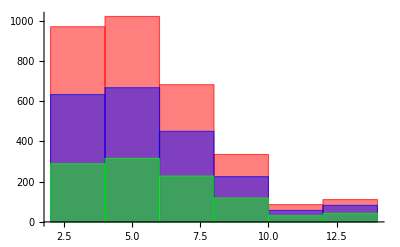

```mathematica
perimeters1=(Select[table,FreeQ[#,"-"]&]//Transpose)⟦1⟧;
perimeters2=(Select[table~Join~table2,FreeQ[#,"-"]&]//Transpose)⟦1⟧;
perimeters3=(Select[table~Join~table2~Join~table3,FreeQ[#,"-"]&]//Transpose)⟦1⟧;
differences1=Table[perimeters1⟦i+1⟧-perimeters1⟦i⟧,{i,1,Length[perimeters1]-1}];
differences2=Table[perimeters2⟦i+1⟧-perimeters2⟦i⟧,{i,1,Length[perimeters2]-1}];
differences3=Table[perimeters3⟦i+1⟧-perimeters3⟦i⟧,{i,1,Length[perimeters3]-1}];
Histogram[{differences3,differences2,differences1},ChartStyle->{Red,Blue,Green}]
```

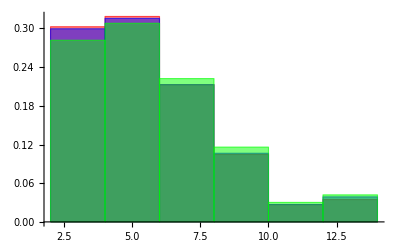

```mathematica
Histogram[{differences3,differences2,differences1},Automatic,"Probability",ChartStyle->{Red,Blue,Green}]
```

## Problem 10 - Summation of primes

The sum of the primes below 10 is 2 + 3 + 5 + 7 = 17.
Find the sum of all the primes below two million.

```mathematica
max=2 10^6;
Plus@@(Select[Prime[Range[max]],#<max&])
```

142913828922

## Problem 11 - Largest product in a grid

In the 20×20 grid below, four numbers along a diagonal line have been marked in red.

08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08
49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00
81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65
52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91
22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80
24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50
32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70
67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21
24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72
21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95
78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92
16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57
86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58
19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40
04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66
88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69
04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36
20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16
20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54
01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48

The product of these numbers is 26 × 63 × 78 × 14 = 1788696.
What is the greatest product of four adjacent numbers in the same direction (up, down, left, right, or diagonally) in the 20×20 grid?

```mathematica
list=ReleaseHold@(List@@@Hold[08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08
49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00
81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65
52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91
22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80
24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50
32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70
67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21
24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72
21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95
78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92
16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57
86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58
19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40
04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66
88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69
04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36
20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16
20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54
01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48]);
```

```mathematica
matrix=Table[list⟦1+20i;;20+20 i⟧,{i,0,19}];
```

```mathematica
lineSearch=Max[Table[Times@@matrix⟦Range[i,i+3],j⟧,{i,1,17},{j,1,20}]];
columnSearch=Max[Table[Times@@(matrix//Transpose)⟦Range[i,i+3],j⟧,{i,1,17},{j,1,20}]];
NorthWestSouthEast=Max[Table[matrix⟦i,j⟧matrix⟦i+1,j+1⟧matrix⟦i+2,j+2⟧matrix⟦i+3,j+3⟧,{i,1,17},{j,1,17}]];
SouthWestNorthEast=Max[Table[matrix⟦i,j⟧matrix⟦i+1,j-1⟧matrix⟦i+2,j-2⟧matrix⟦i+3,j-3⟧,{i,1,17},{j,4,20}]];
Max[{lineSearch,columnSearch,NorthWestSouthEast,SouthWestNorthEast}]
```

70600674

## Problem 12 - Highly divisible triangular number

The sequence of triangle numbers is generated by adding the natural numbers. So the 7th triangle number would be 1 + 2 + 3 + 4 + 5 + 6 + 7 = 28. The first ten terms would be:
1, 3, 6, 10, 15, 21, 28, 36, 45, 55, ...
Let us list the factors of the first seven triangle numbers:
 1: 1
 3: 1,3
 6: 1,2,3,6
10: 1,2,5,10
15: 1,3,5,15
21: 1,3,7,21
28: 1,2,4,7,14,28
We can see that 28 is the first triangle number to have over five divisors.
What is the value of the first triangle number to have over five hundred divisors?

```mathematica
SetAttributes[triangularNumber,Listable]
triangularNumber[k_]:=1/2 k (1+k)
```

```mathematica
max=100000;
divisors=Length/@Divisors@triangularNumber[Range[max]];
triangularNumber[Position[divisors,Select[divisors,(#>500)&]//First]//First]⟦1⟧
```

76576500

## Problem 13 - Large sum

Work out the first ten digits of the sum of the following one-hundred 50-digit numbers.
37107287533902102798797998220837590246510135740250
46376937677490009712648124896970078050417018260538
74324986199524741059474233309513058123726617309629
91942213363574161572522430563301811072406154908250
23067588207539346171171980310421047513778063246676
89261670696623633820136378418383684178734361726757
28112879812849979408065481931592621691275889832738
44274228917432520321923589422876796487670272189318
47451445736001306439091167216856844588711603153276
70386486105843025439939619828917593665686757934951
62176457141856560629502157223196586755079324193331
64906352462741904929101432445813822663347944758178
92575867718337217661963751590579239728245598838407
58203565325359399008402633568948830189458628227828
80181199384826282014278194139940567587151170094390
35398664372827112653829987240784473053190104293586
86515506006295864861532075273371959191420517255829
71693888707715466499115593487603532921714970056938
54370070576826684624621495650076471787294438377604
53282654108756828443191190634694037855217779295145
36123272525000296071075082563815656710885258350721
45876576172410976447339110607218265236877223636045
17423706905851860660448207621209813287860733969412
81142660418086830619328460811191061556940512689692
51934325451728388641918047049293215058642563049483
62467221648435076201727918039944693004732956340691
15732444386908125794514089057706229429197107928209
55037687525678773091862540744969844508330393682126
18336384825330154686196124348767681297534375946515
80386287592878490201521685554828717201219257766954
78182833757993103614740356856449095527097864797581
16726320100436897842553539920931837441497806860984
48403098129077791799088218795327364475675590848030
87086987551392711854517078544161852424320693150332
59959406895756536782107074926966537676326235447210
69793950679652694742597709739166693763042633987085
41052684708299085211399427365734116182760315001271
65378607361501080857009149939512557028198746004375
35829035317434717326932123578154982629742552737307
94953759765105305946966067683156574377167401875275
88902802571733229619176668713819931811048770190271
25267680276078003013678680992525463401061632866526
36270218540497705585629946580636237993140746255962
24074486908231174977792365466257246923322810917141
91430288197103288597806669760892938638285025333403
34413065578016127815921815005561868836468420090470
23053081172816430487623791969842487255036638784583
11487696932154902810424020138335124462181441773470
63783299490636259666498587618221225225512486764533
67720186971698544312419572409913959008952310058822
95548255300263520781532296796249481641953868218774
76085327132285723110424803456124867697064507995236
37774242535411291684276865538926205024910326572967
23701913275725675285653248258265463092207058596522
29798860272258331913126375147341994889534765745501
18495701454879288984856827726077713721403798879715
38298203783031473527721580348144513491373226651381
34829543829199918180278916522431027392251122869539
40957953066405232632538044100059654939159879593635
29746152185502371307642255121183693803580388584903
41698116222072977186158236678424689157993532961922
62467957194401269043877107275048102390895523597457
23189706772547915061505504953922979530901129967519
86188088225875314529584099251203829009407770775672
11306739708304724483816533873502340845647058077308
82959174767140363198008187129011875491310547126581
97623331044818386269515456334926366572897563400500
42846280183517070527831839425882145521227251250327
55121603546981200581762165212827652751691296897789
32238195734329339946437501907836945765883352399886
75506164965184775180738168837861091527357929701337
62177842752192623401942399639168044983993173312731
32924185707147349566916674687634660915035914677504
99518671430235219628894890102423325116913619626622
73267460800591547471830798392868535206946944540724
76841822524674417161514036427982273348055556214818
97142617910342598647204516893989422179826088076852
87783646182799346313767754307809363333018982642090
10848802521674670883215120185883543223812876952786
71329612474782464538636993009049310363619763878039
62184073572399794223406235393808339651327408011116
66627891981488087797941876876144230030984490851411
60661826293682836764744779239180335110989069790714
85786944089552990653640447425576083659976645795096
66024396409905389607120198219976047599490197230297
64913982680032973156037120041377903785566085089252
16730939319872750275468906903707539413042652315011
94809377245048795150954100921645863754710598436791
78639167021187492431995700641917969777599028300699
15368713711936614952811305876380278410754449733078
40789923115535562561142322423255033685442488917353
44889911501440648020369068063960672322193204149535
41503128880339536053299340368006977710650566631954
81234880673210146739058568557934581403627822703280
82616570773948327592232845941706525094512325230608
22918802058777319719839450180888072429661980811197
77158542502016545090413245809786882778948721859617
72107838435069186155435662884062257473692284509516
20849603980134001723930671666823555245252804609722
53503534226472524250874054075591789781264330331690

```mathematica
numbers="37107287533902102798797998220837590246510135740250
46376937677490009712648124896970078050417018260538
74324986199524741059474233309513058123726617309629
91942213363574161572522430563301811072406154908250
23067588207539346171171980310421047513778063246676
89261670696623633820136378418383684178734361726757
28112879812849979408065481931592621691275889832738
44274228917432520321923589422876796487670272189318
47451445736001306439091167216856844588711603153276
70386486105843025439939619828917593665686757934951
62176457141856560629502157223196586755079324193331
64906352462741904929101432445813822663347944758178
92575867718337217661963751590579239728245598838407
58203565325359399008402633568948830189458628227828
80181199384826282014278194139940567587151170094390
35398664372827112653829987240784473053190104293586
86515506006295864861532075273371959191420517255829
71693888707715466499115593487603532921714970056938
54370070576826684624621495650076471787294438377604
53282654108756828443191190634694037855217779295145
36123272525000296071075082563815656710885258350721
45876576172410976447339110607218265236877223636045
17423706905851860660448207621209813287860733969412
81142660418086830619328460811191061556940512689692
51934325451728388641918047049293215058642563049483
62467221648435076201727918039944693004732956340691
15732444386908125794514089057706229429197107928209
55037687525678773091862540744969844508330393682126
18336384825330154686196124348767681297534375946515
80386287592878490201521685554828717201219257766954
78182833757993103614740356856449095527097864797581
16726320100436897842553539920931837441497806860984
48403098129077791799088218795327364475675590848030
87086987551392711854517078544161852424320693150332
59959406895756536782107074926966537676326235447210
69793950679652694742597709739166693763042633987085
41052684708299085211399427365734116182760315001271
65378607361501080857009149939512557028198746004375
35829035317434717326932123578154982629742552737307
94953759765105305946966067683156574377167401875275
88902802571733229619176668713819931811048770190271
25267680276078003013678680992525463401061632866526
36270218540497705585629946580636237993140746255962
24074486908231174977792365466257246923322810917141
91430288197103288597806669760892938638285025333403
34413065578016127815921815005561868836468420090470
23053081172816430487623791969842487255036638784583
11487696932154902810424020138335124462181441773470
63783299490636259666498587618221225225512486764533
67720186971698544312419572409913959008952310058822
95548255300263520781532296796249481641953868218774
76085327132285723110424803456124867697064507995236
37774242535411291684276865538926205024910326572967
23701913275725675285653248258265463092207058596522
29798860272258331913126375147341994889534765745501
18495701454879288984856827726077713721403798879715
38298203783031473527721580348144513491373226651381
34829543829199918180278916522431027392251122869539
40957953066405232632538044100059654939159879593635
29746152185502371307642255121183693803580388584903
41698116222072977186158236678424689157993532961922
62467957194401269043877107275048102390895523597457
23189706772547915061505504953922979530901129967519
86188088225875314529584099251203829009407770775672
11306739708304724483816533873502340845647058077308
82959174767140363198008187129011875491310547126581
97623331044818386269515456334926366572897563400500
42846280183517070527831839425882145521227251250327
55121603546981200581762165212827652751691296897789
32238195734329339946437501907836945765883352399886
75506164965184775180738168837861091527357929701337
62177842752192623401942399639168044983993173312731
32924185707147349566916674687634660915035914677504
99518671430235219628894890102423325116913619626622
73267460800591547471830798392868535206946944540724
76841822524674417161514036427982273348055556214818
97142617910342598647204516893989422179826088076852
87783646182799346313767754307809363333018982642090
10848802521674670883215120185883543223812876952786
71329612474782464538636993009049310363619763878039
62184073572399794223406235393808339651327408011116
66627891981488087797941876876144230030984490851411
60661826293682836764744779239180335110989069790714
85786944089552990653640447425576083659976645795096
66024396409905389607120198219976047599490197230297
64913982680032973156037120041377903785566085089252
16730939319872750275468906903707539413042652315011
94809377245048795150954100921645863754710598436791
78639167021187492431995700641917969777599028300699
15368713711936614952811305876380278410754449733078
40789923115535562561142322423255033685442488917353
44889911501440648020369068063960672322193204149535
41503128880339536053299340368006977710650566631954
81234880673210146739058568557934581403627822703280
82616570773948327592232845941706525094512325230608
22918802058777319719839450180888072429661980811197
77158542502016545090413245809786882778948721859617
72107838435069186155435662884062257473692284509516
20849603980134001723930671666823555245252804609722
53503534226472524250874054075591789781264330331690";
```

```mathematica
size=50;
Plus@@(Table[StringTake[numbers,{i,i+size}]//ToExpression,{i,1,StringLength[numbers]-(size+1),size+1}]~Join~{StringTake[numbers,{StringLength[numbers]-size,StringLength[numbers]}]//ToExpression})//N[#,10]&
```

5.53737623×10^51

## Problem 14 - Longest Collatz sequence

The following iterative sequence is defined for the set of positive integers:
n → n/2 (n is even)
n → 3n + 1 (n is odd)
Using the rule above and starting with 13, we generate the following sequence:
13 → 40 → 20 → 10 → 5 → 16 → 8 → 4 → 2 → 1
It can be seen that this sequence (starting at 13 and finishing at 1) contains 10 terms. Although it has not been proved yet (Collatz Problem), it is thought that all starting numbers finish at 1.
Which starting number, under one million, produces the longest chain?
NOTE: Once the chain starts the terms are allowed to go above one million.

### Solution 1

```mathematica
collatz[n_?EvenQ]:=n/2
collatz[n_?OddQ]:=3n+1
SetAttributes[sequence,Listable]
sequence[starting_]:=NestWhileList[collatz,starting,#≠1&]
seq=Block[{},
Parallelize[Length/@sequence[Range[1000000]]];
Position[seq,Max[seq]]
]//AbsoluteTiming
```

{312.756,{{}}}

### Solution 2

```mathematica
collatz[n_?EvenQ]:=n/2
collatz[n_?OddQ]:=3n+1
SetAttributes[sequence,Listable]
sequence[starting_]:=(sequence[starting]={starting}~Join~sequence[collatz[starting]])
sequence[2]={1};
seq=Block[{},
Parallelize[Length/@sequence[Range[1000000]]];
Position[seq,Max[seq]]
]//AbsoluteTiming
```

{74.1491,{{}}}

## Problem 15 - Lattice paths

Starting in the top left corner of a 2×2 grid, and only being able to move to the right and down, there are exactly 6 routes to the bottom right corner.

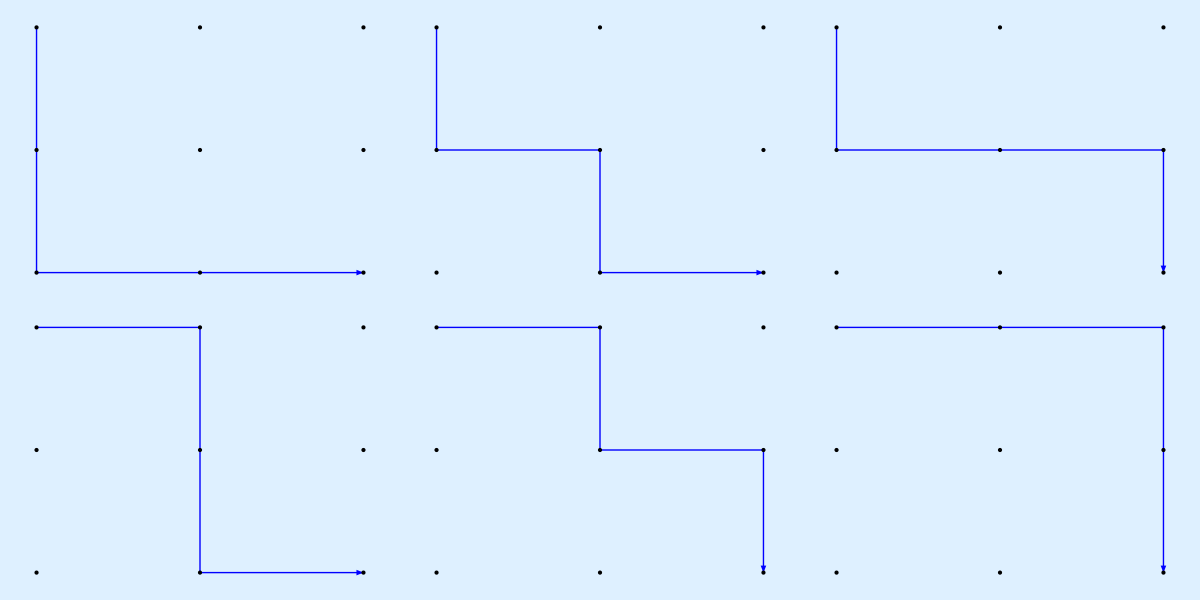

```mathematica
lattice=Table[{i,j},{i,0,2},{j,0,-2,-1}];
paths={
{{0,0},{0,-1},{0,-2},{1,-2},{2,-2}},
{{0,0},{0,-1},{1,-1},{1,-2},{2,-2}},
{{0,0},{0,-1},{1,-1},{2,-1},{2,-2}},
{{0,0},{1,0},{1,-1},{1,-2},{2,-2}},
{{0,0},{1,0},{1,-1},{2,-1},{2,-2}},
{{0,0},{1,0},{2,0},{2,-1},{2,-2}}
};
figure=Table[Show[Graphics[{Arrowheads[Medium],Blue,Thick,#}]&@((Arrow/@paths)⟦i⟧),Graphics[{PointSize[Large],#}]&@(Point/@lattice),Background->LightBlue],{i,Length[paths]}];
{figure⟦1;;3⟧,figure⟦4;;6⟧}//Grid
```

How many such routes are there through a 20×20 grid?

```mathematica
Binomial[40,20]
```

137846528820

## Problem 16 - Power digit sum

2^15 = 32768 and the sum of its digits is 3 + 2 + 7 + 6 + 8 = 26.
What is the sum of the digits of the number 2^1000?

```mathematica
Plus@@IntegerDigits[2^1000]
```

1366

## Problem 17 - Number letter counts

If the numbers 1 to 5 are written out in words: one, two, three, four, five, then there are 3 + 3 + 5 + 4 + 4 = 19 letters used in total.
If all the numbers from 1 to 1000 (one thousand) inclusive were written out in words, how many letters would be used?

NOTE: Do not count spaces or hyphens. For example, 342 (three hundred and forty-two) contains 23 letters and 115 (one hundred and fifteen) contains 20 letters. The use of “and” when writing out numbers is in compliance with British usage.

```mathematica
Print[Style["The answer is "<>ToString@#<>".",18,Blue,Bold,FontFamily->"Georgia"]]&@((Plus@@Table[StringLength@StringReplace[IntegerName[i,"Words"],{" "->"","-"->""}],{i,1,1000}])+9 99 3)
```

The answer is 21124.

Note: the extra term of 9 x 99 x 3 is needed to take into account the “and”s missing in our couting. The first 9 is due to the fact that we have “and”s in all the nine hundreds. Looking at a particular hundred, 200 for example, the 99 is couting the fact that we only don’t have an “and” when we have the 200 itself, but we do have for 201, 202, ..., 246 and etc. The 3 is counting the size of “and”.

## Problem 18 - Maximum path sum I

By starting at the top of the triangle below and moving to adjacent numbers on the row below, the maximum total from top to bottom is 23.

3
7 4
2 4 6
8 5 9 3

That is, 3 + 7 + 4 + 9 = 23.
Find the maximum total from top to bottom of the triangle below:

75
95 64
17 47 82
18 35 87 10
20 04 82 47 65
19 01 23 75 03 34
88 02 77 73 07 63 67
99 65 04 28 06 16 70 92
41 41 26 56 83 40 80 70 33
41 48 72 33 47 32 37 16 94 29
53 71 44 65 25 43 91 52 97 51 14
70 11 33 28 77 73 17 78 39 68 17 57
91 71 52 38 17 14 91 43 58 50 27 29 48
63 66 04 68 89 53 67 30 73 16 69 87 40 31
04 62 98 27 23 09 70 98 73 93 38 53 60 04 23

NOTE: As there are only 16384 routes, it is possible to solve this problem by trying every route. However, Problem 67, is the same challenge with a triangle containing one-hundred rows; it cannot be solved by brute force, and requires a clever method! ;o)

```mathematica
weights=ReleaseHold[List@@@Hold[75
95 64
17 47 82
18 35 87 10
20 04 82 47 65
19 01 23 75 03 34
88 02 77 73 07 63 67
99 65 04 28 06 16 70 92
41 41 26 56 83 40 80 70 33
41 48 72 33 47 32 37 16 94 29
53 71 44 65 25 43 91 52 97 51 14
70 11 33 28 77 73 17 78 39 68 17 57
91 71 52 38 17 14 91 43 58 50 27 29 48
63 66 04 68 89 53 67 30 73 16 69 87 40 31
04 62 98 27 23 09 70 98 73 93 38 53 60 04 23]];
```

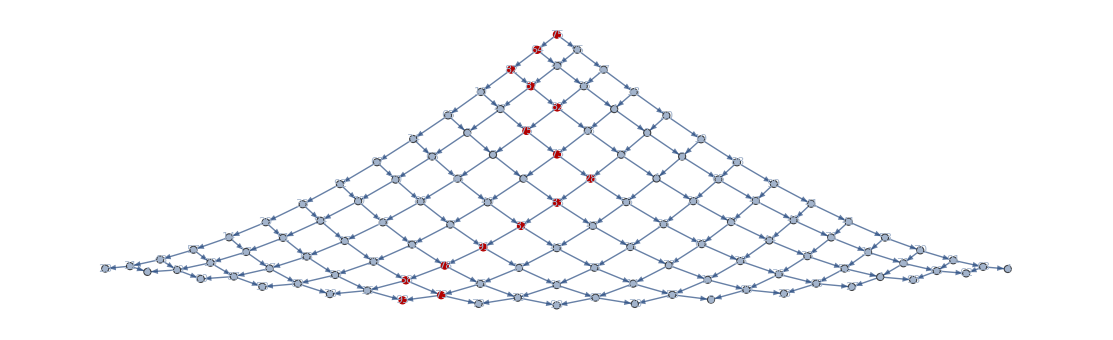

The maximum total from top to bottom is 1074.

```mathematica
levels=15;
vertices=Table[v[i,j],{i,1,levels},{j,1,i}]//Flatten;
edges=Table[{v[i,j]->v[i+1,j],v[i,j]->v[i+1,j+1]},{i,1,levels-1},{j,1,i}]//Flatten;
atributeWeights=MapThread[#1->#2&,{vertices,weights}];
tree=Graph[
Table[v[i,j],{i,1,levels},{j,1,i}]//Flatten,
edges,
VertexWeight->weights,
VertexSize->Large,
VertexLabels->{Placed["VertexWeight",Center]}
];
allpaths=Table[FindPath[tree,v[1,1],v[levels,i],∞,All],{i,1,levels}]//Flatten[#,1]&;
res=Plus@@@(allpaths/.atributeWeights)//Max;
maxpath=Take[allpaths,Position[Plus@@@(allpaths/.atributeWeights),Plus@@@(allpaths/.atributeWeights)//Max]//First];
HighlightGraph[tree,PathGraph[maxpath//First]]
Print["The maximum total from top to bottom is ",res,"."]
```

## Problem 19 - Counting Sundays

You are given the following information, but you may prefer to do some research for yourself.
	•	1 Jan 1900 was a Monday.
	•	Thirty days has September, 
		April, June and November.
		All the rest have thirty-one,
		Saving February alone,
		Which has twenty-eight, rain or shine.
		And on leap years, twenty-nine.
	•	A leap year occurs on any year evenly divisible by 4, but not on a century unless it is divisible by 400.
How many Sundays fell on the first of the month during the twentieth century (1 Jan 1901 to 31 Dec 2000)?

```mathematica
january=Range[31];
february[year_]:=If[(Mod[year,4]==0∧Mod[year,100]≠0)∨(Mod[year,4]==0∧Mod[year,400]==0),Range[29],Range[28]]
march=Range[31];
april=Range[30];
may=Range[31];
june=Range[30];
july=Range[31];
august=Range[31];
september=Range[30];
october=Range[31];
november=Range[30];
december=Range[31];
year[n_]:={january,february[n],march,april,may,june,july,august,september,october,november,december}//Flatten
years=Table[year[n],{n,1901,2000,1}]//Flatten;
alldays=Table[Mod[i,7,1],{i,2,Length[years]+1}]//Flatten;
res=Count[MapThread[{#1,#2}&,{alldays,years}],{7,1}];
Print[Style[ToString@res<>" Sundays fell on the first of the month during the twentieth century.",Red,FontFamily->"Times New Roman",18]]
```

171 Sundays fell on the first of the month during the twentieth century.

## Problem 20 - Factorial digit sum

n! means n × (n − 1) × ... × 3 × 2 × 1
For example, 10! = 10 × 9 × ... × 3 × 2 × 1 = 3628800,
and the sum of the digits in the number 10! is 3 + 6 + 2 + 8 + 8 + 0 + 0 = 27.
Find the sum of the digits in the number 100!

```mathematica
Plus@@IntegerDigits[100!]
```

648

## Problem 21 - Amicable numbers

Let d(n) be defined as the sum of proper divisors of n (numbers less than n which divide evenly into n).
If d(a) = b and d(b) = a, where a ≠ b, then a and b are an amicable pair and each of a and b are called amicable numbers.
For example, the proper divisors of 220 are 1, 2, 4, 5, 10, 11, 20, 22, 44, 55 and 110; therefore d(220) = 284. The proper divisors of 284 are 1, 2, 4, 71 and 142; so d(284) = 220.
Evaluate the sum of all the amicable numbers under 10000.

```mathematica
SetAttributes[d,Listable]
d[n_]:=Plus@@Drop[Divisors[n],-1]
d[0]=0;
almostAmicable=(Position[d[d[Range[9999]]]-Range[9999],0]//Flatten)
amicable=Block[{temp=almostAmicable},
While[!FreeQ[d@temp-temp,0],temp=Drop[temp,Position[d@temp-temp,0]//First]];
temp
]
Plus@@amicable
```

{6,28,220,284,496,1184,1210,2620,2924,5020,5564,6232,6368,8128}

{220,284,1184,1210,2620,2924,5020,5564,6232,6368}

31626

## Problem 22 - Names scores

Using names.txt (right click and ‘Save Link/Target As...’), a 46K text file containing over five-thousand first names, begin by sorting it into alphabetical order. Then working out the alphabetical value for each name, multiply this value by its alphabetical position in the list to obtain a name score.
For example, when the list is sorted into alphabetical order, COLIN, which is worth 3 + 15 + 12 + 9 + 14 = 53, is the 938th name in the list. So, COLIN would obtain a score of 938 × 53 = 49714.
What is the total of all the name scores in the file?

```mathematica
names=Import["https://projecteuler.net/project/resources/p022_names.txt"];
names=ImportString[StringReplace[names,{"\""->"",","->"\n "}],"Table"]//Flatten;
```

```mathematica
sortedNames=Sort@names;
Plus@@(Plus@@@LetterNumber/@Characters[sortedNames⟦Range[Length[sortedNames]]⟧]Range[Length[sortedNames]])
```

871198282

## Problem 23 - Non-abundant sums (To be Optimized)

A perfect number is a number for which the sum of its proper divisors is exactly equal to the number. For example, the sum of the proper divisors of 28 would be 1 + 2 + 4 + 7 + 14 = 28, which means that 28 is a perfect number.
A number n is called deficient if the sum of its proper divisors is less than n and it is called abundant if this sum exceeds n.
As 12 is the smallest abundant number, 1 + 2 + 3 + 4 + 6 = 16, the smallest number that can be written as the sum of two abundant numbers is 24. By mathematical analysis, it can be shown that all integers greater than 28123 can be written as the sum of two abundant numbers. However, this upper limit cannot be reduced any further by analysis even though it is known that the greatest number that cannot be expressed as the sum of two abundant numbers is less than this limit.
Find the sum of all the positive integers which cannot be written as the sum of two abundant numbers.

```mathematica
SetAttributes[abundantQ,Listable]
abundantQ[n_Integer]:=((Plus@@Drop[Divisors[n],-1])>n)
sumOfTwo[n_Integer]:=Table[{i,n-i},{i,1,n/2//Floor}];
SetSharedVariable[j]
Monitor[table=ParallelTable[j=i;FreeQ[abundantQ/@sumOfTwo[i],{True,True}],{i,28123}];,ProgressIndicator[j,{1,28123}]]
```

```mathematica
Plus@@(Position[table,True]//Flatten)
```

4179871

## Problem 24 - Lexicographic permutations

A permutation is an ordered arrangement of objects. For example, 3124 is one possible permutation of the digits 1, 2, 3 and 4. If all of the permutations are listed numerically or alphabetically, we call it lexicographic order. The lexicographic permutations of 0, 1 and 2 are:
012   021   102   120   201   210
What is the millionth lexicographic permutation of the digits 0, 1, 2, 3, 4, 5, 6, 7, 8 and 9?

```mathematica
Sort[FromDigits/@Permutations[Range[0,9]]]⟦1000000⟧
```

2783915460

## Problem 25 - 1000-digit Fibonacci number

The Fibonacci sequence is defined by the recurrence relation:
F_n = F_(n-1) + F_(n-2), where F_1 = 1 and F_2 = 1.
Hence the first 12 terms will be:
F_1 = 1
F_2 = 1
F_3 = 2
F_4 = 3
F_5 = 5
F_6 = 8
F_7 = 13
F_8 = 21
F_9 = 34
F_10 = 55
F_11 = 89
F_12 = 144
The 12th term, F_12, is the first term to contain three digits.
What is the index of the first term in the Fibonacci sequence to contain 1000 digits?

```mathematica
Block[{n=1000},
While[(IntegerDigits[Fibonacci[n]]//Length)<1000,n++];
n
]
```

4782

## Problem 26 - Reciprocal cycles

A unit fraction contains 1 in the numerator. The decimal representation of the unit fractions with denominators 2 to 10 are given:
1/2 = 0.5
1/3= 0.(3)
1/4= 0.25
1/5= 0.2
1/6= 0.1(6)
1/7= 0.(142857)
1/8= 0.125
1/9= 0.(1)
1/10= 0.1
Where 0.1(6) means 0.166666..., and has a 1-digit recurring cycle. It can be seen that 1/7 has a 6-digit recurring cycle.
Find the value of d < 1000 for which 1/d contains the longest recurring cycle in its decimal fraction part.

```mathematica
table=Table[Length@RealDigits[1/n]⟦1,1⟧,{n,1,999}];
Position[table,Max[table]]
```

{{983}}

## Problem 27 - Quadratic primes

Euler discovered the remarkable quadratic formula:
n.b2 + n + 41
It turns out that the formula will produce 40 primes for the consecutive values n = 0 to 39. However, when n = 40, 402 + 40 + 41 = 40(40 + 1) + 41 is divisible by 41, and certainly when n = 41, 41.b2 + 41 + 41 is clearly divisible by 41.
The incredible formula  n.b2 − 79n + 1601 was discovered, which produces 80 primes for the consecutive values n = 0 to 79. The product of the coefficients, −79 and 1601, is −126479.
Considering quadratics of the form:
n.b2 + an + b, where |a| < 1000 and |b| < 1000
where |n| is the modulus/absolute value of n
e.g. |11| = 11 and |−4| = 4
Find the product of the coefficients, a and b, for the quadratic expression that produces the maximum number of primes for consecutive values of n, starting with n = 0.

```mathematica
max=100;
SetAttributes[primeQuadratic,Listable]
primeQuadratic[a_,b_,n_]:=n^2+a n+b
initialCheck[a_,b_]:=And@@(PrimeQ@primeQuadratic[a,b,Range[0,5]])
primeQ[a_,b_]:=PrimeQ[primeQuadratic[a,b,Range[0,max]]]
numberOfPrimes[a_,b_]:=Drop[primeQ[a,b],((Position[primeQ[a,b],False]//First)-{max+2})//First]//Length
```

```mathematica
check=ParallelTable[initialCheck[a,b],{a,-999,999},{b,-999,999}];
listCoefficients=Position[check,True]-Table[{1000,1000},{Length@Position[check,True]}];
max=Table[numberOfPrimes[Sequence@@listCoefficients⟦i⟧],{i,1,Length[listCoefficients]}]//Max
Times@@listCoefficients⟦Position[Table[numberOfPrimes[Sequence@@listCoefficients⟦i⟧],{i,1,Length[listCoefficients]}],max]//First//First⟧
```

71

-59231

## Problem 28 - Number spiral diagonals

Starting with the number 1 and moving to the right in a clockwise direction a 5 by 5 spiral is formed as follows:

21 22 23 24 25
20  7  8  9 10
19  6  1  2 11
18  5  4  3 12
17 16 15 14 13

It can be verified that the sum of the numbers on the diagonals is 101.
What is the sum of the numbers on the diagonals in a 1001 by 1001 spiral formed in the same way?

```mathematica
spiralMatrix[n_?OddQ]:=Table[v[i,j],{i,-Floor[n/2],Floor[n/2]},{j,-Floor[n/2],Floor[n/2]}]
spiralElements[n_?OddQ]:=Block[{i=1,list={{0,0}}},
While[Length[list]<n^2,
list=list~Join~Table[(list//Last)+{0,j},{j,i}];
list=list~Join~Table[(list//Last)+{j,0},{j,i}];
i++;
list=list~Join~Table[(list//Last)-{0,j},{j,i}];
list=list~Join~Table[(list//Last)-{j,0},{j,i}];
i++;
]
Take[list,n^2]/.Null->1
]
substitutionRule[n_?OddQ]:=MapThread[#1->#2&,{v@@@spiralElements[n],Range[n^2]}]
spiral[n_?OddQ]:=spiralMatrix[n]/.substitutionRule[n]
spiral[9]//TableForm
```

73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81
72 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
71 | 42 | 21 | 22 | 23 | 24 | 25 | 26 | 51
70 | 41 | 20 | 7 | 8 | 9 | 10 | 27 | 52
69 | 40 | 19 | 6 | 1 | 2 | 11 | 28 | 53
68 | 39 | 18 | 5 | 4 | 3 | 12 | 29 | 54
67 | 38 | 17 | 16 | 15 | 14 | 13 | 30 | 55
66 | 37 | 36 | 35 | 34 | 33 | 32 | 31 | 56
65 | 64 | 63 | 62 | 61 | 60 | 59 | 58 | 57

```mathematica
ClearAll[diagonal,secDiagonal]
diagonal[n_]:=diagonal[n]=diagonal[n-1]~Join~{(diagonal[n-1]//Last)+2(n-1)}
diagonal[1]={1};
ClearAll[secDiagonal]
secDiagonal[n_]:=secDiagonal[n]=secDiagonal[n-2]~Join~{(secDiagonal[n-2]//Last)+4((n-1)/2),(secDiagonal[n-2]//Last)+8((n-1)/2)}
secDiagonal[1]={1};
```

```mathematica
(Plus@@diagonal[1001])+(Plus@@secDiagonal[1001])-1
```

669171001

## Problem 29 - Distinct Powers

Consider all integer combinations of ab for 2 ≤ a ≤ 5 and 2 ≤ b ≤ 5:
2^2=4, 2^3=8, 2^4=16, 2^5=32
3^2=9, 3^3=27, 3^4=81, 3^5=243
4^2=16, 4^3=64, 4^4=256, 4^5=1024
5^2=25, 5^3=125, 5^4=625, 5^5=3125
If they are then placed in numerical order, with any repeats removed, we get the following sequence of 15 distinct terms:

4, 8, 9, 16, 25, 27, 32, 64, 81, 125, 243, 256, 625, 1024, 3125

How many distinct terms are in the sequence generated by a^b for 2 ≤ a ≤ 100 and 2 ≤ b ≤ 100?

```mathematica
Table[a^b,{a,2,100},{b,2,100}]//Flatten//Union//Length
```

9183

## Problem 30 - Digit fifth powers

Surprisingly there are only three numbers that can be written as the sum of fourth powers of their digits:
1634 = 1^4 + 6^4 + 3^4 + 4^4
8208 = 8^4 + 2^4 + 0^4 + 8^4
9474 = 9^4 + 4^4 + 7^4 + 4^4
As 1 = 1^4 is not a sum it is not included.
The sum of these numbers is 1634 + 8208 + 9474 = 19316.
Find the sum of all the numbers that can be written as the sum of fifth powers of their digits.

```mathematica
Plus@@(Position[Table[Plus@@(IntegerDigits[n]^5)==n,{n,1,1000000}],True]//Flatten)-1
```

443839

## Problem 31 - Coin sums

In England the currency is made up of pound, £, and pence, p, and there are eight coins in general circulation:
1p, 2p, 5p, 10p, 20p, 50p, £1 (100p) and £2 (200p).
It is possible to make £2 in the following way:
1×£1 + 1×50p + 2×20p + 1×5p + 1×2p + 3×1p
How many different ways can £2 be made using any number of coins?

```mathematica
FrobeniusSolve[{1,2,5,10,20,50,100,200},200]//Length
```

73682

## Problem 32 - Pandigital products

We shall say that an n-digit number is pandigital if it makes use of all the digits 1 to n exactly once; for example, the 5-digit number, 15234, is 1 through 5 pandigital.
The product 7254 is unusual, as the identity, 39 × 186 = 7254, containing multiplicand, multiplier, and product is 1 through 9 pandigital.
Find the sum of all products whose multiplicand/multiplier/product identity can be written as a 1 through 9 pandigital.
HINT: Some products can be obtained in more than one way so be sure to only include it once in your sum.

```mathematica
product1per4[list_]:=FromDigits[Take[list,1]]FromDigits[Take[list,{2,5}]]==fromList[Take[list,{6,9}]]
product2per3[list_]:=FromDigits[Take[list,{1,2}]]FromDigits[Take[list,{3,5}]]==fromList[Take[list,{6,9}]]
```

```mathematica
possiblePermutations=Permutations@Range[9];
```

```mathematica
case1=Flatten@Position[product1per4/@possiblePermutations,True]
```

{124050,125682}

```mathematica
case2=Flatten[Position[product2per3/@possiblePermutations,True]]
```

{1204,30949,66229,70880,116612,126076,151560}

```mathematica
Total[Union[(fromList[Take[possiblePermutations⟦#⟧,{6,9}]]&/@case1)~Join~(fromList[Take[possiblePermutations⟦#⟧,{6,9}]]&/@case2)]]
```

45228

## Problem 33 - Digit cancelling fractions

The fraction 49/98 is a curious fraction, as an inexperienced mathematician in attempting to simplify it may incorrectly believe that 49/98 = 4/8, which is correct, is obtained by cancelling the 9s.
We shall consider fractions like, 30/50 = 3/5, to be trivial examples.
There are exactly four non-trivial examples of this type of fraction, less than one in value, and containing two digits in the numerator and denominator.
If the product of these four fractions is given in its lowest common terms, find the value of the denominator.

```mathematica
cancellingFractions[a_,b_]:=Block[{temp={IntegerDigits[a],IntegerDigits[b]},list,pos},
list=Gather[#,#1==#2&]&@(temp//Flatten);
If[
ContainsAny@@temp∧FreeQ[list,0]∧(Union[list]//Length)>2,
pos=Position[list,Select[list,Length[#]==2&]//First]//First;
a/b==Rational@@(Drop[#,pos]&@list//Flatten),
False]
]
```

```mathematica
Times@@Rational@@@Reverse/@Position[Table[cancellingFractions[a,b],{b,1,99},{a,1,b}],True]
```

1/100

## Problem 34 - Digit factorials

145 is a curious number, as 1! + 4! + 5! = 1 + 24 + 120 = 145.
Find the sum of all numbers which are equal to the sum of the factorial of their digits.
Note: as 1! = 1 and 2! = 2 are not sums they are not included.

```mathematica
Plus@@(Drop[Position[Table[n==Plus@@(IntegerDigits[n]!),{n,1,1000000}],True],2]//Flatten)
```

40730

## Problem 35 - Circular primes

The number, 197, is called a circular prime because all rotations of the digits: 197, 971, and 719, are themselves prime.
There are thirteen such primes below 100: 2, 3, 5, 7, 11, 13, 17, 31, 37, 71, 73, 79, and 97.
How many circular primes are there below one million?

```mathematica
circularPrimeQ[n_]:=If[Length@IntegerDigits[n]==1,True,FreeQ[PrimeQ/@(FromDigits/@Permute[IntegerDigits[n],CyclicGroup[Length[IntegerDigits[n]]]]),False]]
```

```mathematica
Count[ParallelTable[circularPrimeQ[Prime[n]],{n,1,78498}],True]
```

55